## Data

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import ["task1.csv"];
claassMinus1=data[[Flatten@Position[data[[All,3]],-1]]];
claassMinus2=data[[Flatten@Position[data[[All,3]],1]]];
n=Length@data;
```

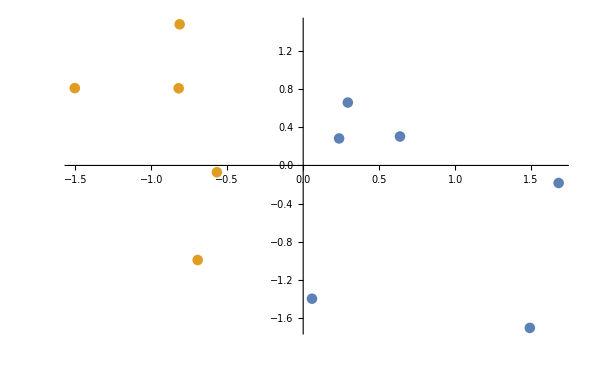

```mathematica
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]]}]
```

```mathematica
alpha=Array[α,n]
```

{α[1],α[2],α[3],α[4],α[5],α[6],α[7],α[8],α[9],α[10],α[11]}

```mathematica
X=data⟦All,;;2⟧
Y=data⟦All,3⟧
```

{{0.0578333,-1.3981},{0.236386,0.283487},{-0.819391,0.809699},{1.49169,-1.70461},{-0.56784,-0.0710002},{-0.694414,-0.992279},{0.293799,0.660239},{-0.813164,1.48096},{-1.5032,0.811566},{0.637056,0.303951},{1.68124,-0.183918}}

{-1,-1,1,-1,1,1,-1,1,1,-1,-1}

```mathematica
L=Total[alpha]-1/2*Sum[alpha⟦i⟧*alpha⟦j⟧*Y⟦i⟧*Y⟦j⟧*(X⟦i⟧.X⟦j⟧),{i,1,n},{j,1,n}];
```

```mathematica
condition=Total[alpha*Y]
```

-α[1]-α[2]+α[3]-α[4]+α[5]+α[6]-α[7]+α[8]+α[9]-α[10]-α[11]

```mathematica
res=NMaximize[{L,alpha≥0,condition==0},alpha]
```

{3.44173,{α[1]→0.890406,α[2]→2.5517,α[3]→0.,α[4]→0.,α[5]→3.44211,α[6]→0.,α[7]→0.,α[8]→0.,α[9]→0.,α[10]→0.,α[11]→0.}}

```mathematica
Y
```

{-1,-1,1,-1,1,1,-1,1,1,-1,-1}

```mathematica
alphaSolve=res[[2]][[All,2]]
```

{0.890406,2.5517,0.,0.,3.44211,0.,0.,0.,0.,0.,0.}

```mathematica
w=Sum[alphaSolve[[i]]*Y[[i]]*X[[i]],{i,1,n}]
```

{-2.60925,0.277109}

```mathematica
b=1/1*Sum[Y[[i]]-(w.X[[i]]),{i,1,1}]
```

-0.461674

```mathematica
plos=b+w.{x1,x2}
```

-0.461674-2.60925 x1+0.277109 x2

```mathematica
resu=First[Flatten@Solve[plos==0,x2]][[2]]//FullSimplify
```

1.66604+9.41598 x1

```mathematica
fun[resu_,x_]:=resu/.{x1->x}
```

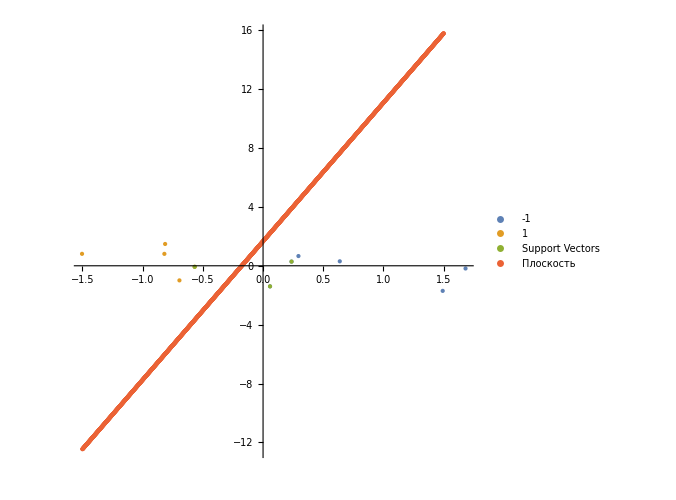

```mathematica
points=Table[{x,fun[resu,x]},{x,-1.5,1.5,0.001}];
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]],{X[[1]],X[[2]],X[[5]]},points},PlotLegends->{-1,1,"Support Vectors","Плоскость"},PlotStyle->PointSize[Large],Joined->{False,False,False},AspectRatio->1,ImageSize->500]
```